# Jeremy — PS 3 — 2025-01-24

### EIWL3 Section 9 Questions

```mathematica
Manipulate[Range[n],{n,0,100}]
```

```mathematica
Manipulate[ListLinePlot[Range[n]],{n,5,100,1}]
```

```mathematica
Manipulate[Column[Table[x,n]],{n,1,10}]
```

```mathematica
Manipulate[Graphics[Style[Disk[],Hue[n]]],{n,0,1}]
```

```mathematica
Manipulate[Graphics[Style[Disk[],RGBColor[a,b,c]]],{a,0,1},{b,0,1},{c,0,1}]
```

```mathematica
Manipulate[IntegerDigits[n],{n,1000,9999,1}]
```

```mathematica
Manipulate[Table[Hue[n],{n,0,1,1/x}],{x,4,49}]
```

```mathematica
Manipulate[Table[Graphics[Style[RegularPolygon[6],Hue[n]]],m],{n,0,1},{m,1,10}]
```

```mathematica
Manipulate[Graphics[Style[RegularPolygon[n],colour]],{n,5,20},{colour,{Red, Yellow, Blue}}]
```

```mathematica
Manipulate[PieChart[Table[1,n]],{n,1,10}]
```

```mathematica
Manipulate[BarChart[IntegerDigits[n]],{n,100,999,1}]
```

```mathematica
Manipulate[Table[RandomColor[],n],{n,1,50}]
```

```mathematica
Manipulate[Column[Table[base^a,{a,1,n,1}]],{n,1,10,1},{base,1,25,1}]
```

```mathematica
Manipulate[NumberLinePlot[Table[x^n,{x,10}]],{n,0,5}]
```

```mathematica
Manipulate[Graphics3D[Style[Sphere[],RGBColor[n,1-n,0]]],{n,0,1}]
```

### EIWL3 Section 10 Questions

```mathematica
ColorNegate[EdgeDetect[-Graphics-]]
```

-Graphics-

```mathematica
Manipulate[Blur[-Graphics-,n],{n,0,20}]
```

```mathematica
Table[EdgeDetect[Blur[-Graphics-,n]],{n,1,10}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ImageCollage[{-Graphics-,Blur[-Graphics-],EdgeDetect[-Graphics-],Binarize[-Graphics-]}]
```

-Graphics-

```mathematica
ImageAdd[Binarize[-Graphics-],-Graphics-]
```

-Graphics-

```mathematica
Manipulate[EdgeDetect[Blur[-Graphics-,n]],{n,0,20}]
```

```mathematica
EdgeDetect[Graphics3D[Sphere[]]]
```

-Graphics-

```mathematica
Manipulate[Blur[Graphics[Style[RegularPolygon[5],Purple]],n],{n,0,20}]
```

```mathematica
ImageCollage[Table[Graphics[Style[Disk[],RandomColor[]]],9]]
```

-Graphics-

```mathematica
ImageCollage[Table[Graphics3D[Style[Sphere[],Hue[n]]],{n,0,1,0.2}]]
```

-Graphics-

```mathematica
Table[Blur[Graphics[Disk[]],n],{n,0,30,5}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ImageAdd[-Graphics-,Graphics[Disk[]]]
```

-Graphics-

```mathematica
ImageAdd[-Graphics-,Graphics[Style[RegularPolygon[8],Red]]]
```

-Graphics-

```mathematica
ImageAdd[-Graphics-,ColorNegate[EdgeDetect[-Graphics-]]]
```

-Graphics-

### EIWL3 Section 11 Questions

```mathematica
StringJoin["Hello","Hello"]
```

HelloHello

```mathematica
ToUpperCase[StringJoin[Alphabet[]]]
```

ABCDEFGHIJKLMNOPQRSTUVWXYZ

```mathematica
StringReverse[StringJoin[Alphabet[]]]
```

zyxwvutsrqponmlkjihgfedcba

```mathematica
StringJoin[Table["AGCT",100]]
```

AGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCT

```mathematica
StringTake[StringJoin[Alphabet[]],6]
```

abcdef

```mathematica
Column[Table[StringTake["this is about strings",n],{n,StringLength["this is about strings"]}]]
```

t
th
thi
this
this 
this i
this is
this is 
this is a
this is ab
this is abo
this is abou
this is about
this is about 
this is about s
this is about st
this is about str
this is about stri
this is about strin
this is about string
this is about strings

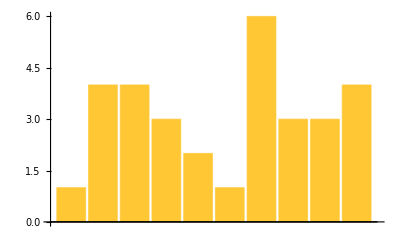

```mathematica
BarChart[StringLength[TextWords["A long time ago, in a galaxy far, far away"]]]
```

```mathematica
StringLength[WikipediaData["computer"]]
```

60266

```mathematica
Length[TextWords[WikipediaData["computer"]]]
```

9271

```mathematica
Take[TextSentences[WikipediaData["strings"]],1]
```

{String or strings may refer to:}

```mathematica
StringJoin[StringTake[TextSentences[WikipediaData["computers"]],1]]
```

AMTTACCESEMTTTCTPP=ITTDBTTTT==DTLTTTSITIIDMTTAAATTTIASIBIAITITIITSI=CCAHTFTTTAEBNH=ITax()2{,THI=DHTTTTAB==CBTDETTITIRTZTT=PTEITDTTHACIINCTLOTIIIHBT==TTHTVTE=ECWATIHJTIIAATBAIL=TJFCJTHATHTTWITT=TTDTKIHKNNHPNIMTGFTTWISTITS=TTLTTTT=C=A=SH=TC==ATIET=WTTSC=TSC=TCATRDIRTPIWJSAIT=TES=TTSHTALTSG=AETTLSIETWOAMTTRACrRIIISFIIG=IDOHCIAMA=WTOBItSTBSIT=SMSTSS=SSCICW=T=TTMIAL=TITHTFMPWSTCBOTOI=ITTSTTITMWITC=PUTTS=MF=ATHHIT=PALTP=ETHOBSA=CTITTITCITA"=AWA=TMH=TQCVSLTTT=ACARPE=AT=====M

```mathematica
Last[Sort[StringLength[WordList[]]]]
```

23

```mathematica
Count[StringTake[WordList[],1],"q"]
```

194

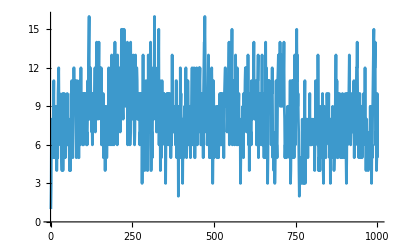

```mathematica
ListLinePlot[StringLength[Take[WordList[],1000]]]
```

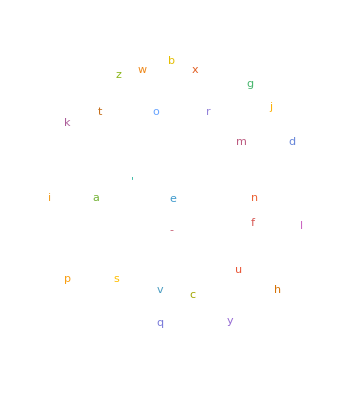

```mathematica
WordCloud[Characters[StringJoin[WordList[]]]]
```